```mathematica
n=10;
α=.01;
β=0;
```

```mathematica
Q[0]=Table[RandomInteger[{1,1000}],{i,1,n}]
```

{959,331,688,423,180,755,982,984,84,777}

```mathematica
x=Table[{RandomReal[{0,100}],RandomReal[{0,100}]},{i,1,n}];
d=Table[EuclideanDistance[x[[i]],x[[j]]],{i,1,n},{j,1,n}];
```

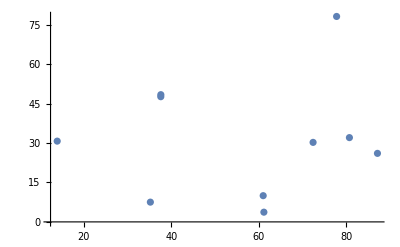

```mathematica
ListPlot[x,PlotRange->All]
```

```mathematica
M1[Q_]:=α*Table[If[j≠i,Boole[Q[[j]]<Q[[i]]]/d[[i,j]],0],{i,1,n},{j,1,n}]
M2[Q_]:=-α*Table[If[j==i,Sum[If[k≠i,Boole[Q[[k]]>Q[[i]]]/d[[i,k]],0],{k,1,n}],0],{i,1,n},{j,1,n}]
M3[Q_]:=β*IdentityMatrix[n]
```

```mathematica
M[Q_]:=M1[Q]+M2[Q]+M3[Q]
```

```mathematica
TraditionalForm[M[Q[0]]]
```

(-0.00134732 | 0.000229447 | 0.000430112 | 0.000254824 | 0.0002076 | 0.000347015 | 0. | 0. | 0.000653645 | 0.000257054
0. | -0.00200123 | 0. | 0. | 0.000121315 | 0. | 0. | 0. | 0.000181416 | 0.
0. | 0.000386003 | -0.00278203 | 0.000222404 | 0.00014252 | 0. | 0. | 0. | 0.000326001 | 0.
0. | 0.000244356 | 0. | -0.014127 | 0.000200072 | 0. | 0. | 0. | 0.000184117 | 0.
0. | 0. | 0. | 0. | -0.00134328 | 0. | 0. | 0. | 0.00018911 | 0.
0. | 0.000381279 | 0.00159392 | 0.000198025 | 0.000131173 | -0.00102193 | 0. | 0. | 0.000291889 | 0.
0.00117635 | 0.000193461 | 0.000337941 | 0.000216947 | 0.00021668 | 0.000290426 | -0.000149682 | 0. | 0.00113976 | 0.000218161
0.000170966 | 0.000317614 | 0.000194372 | 0.000338422 | 0.000125737 | 0.000183765 | 0.000149682 | 0. | 0.000136326 | 0.000343863
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0032874 | 0.
0. | 0.000249071 | 0.000225682 | 0.0128964 | 0.000198186 | 0.00020072 | 0. | 0. | 0.000185145 | -0.000819078)

```mathematica
Eigenvalues[M[Q[0]]]
```

{-0.014127,-0.0032874,-0.00278203,-0.00200123,-0.00134732,-0.00134328,-0.00102193,-0.000819078,-0.000149682,0.}

```mathematica
Q[t_]=FullSimplify[MatrixExp[t*M[Q[0]]].Q[0]];
```

```mathematica
Limit[Q[t],t->Infinity]
```

{6.911×10^-14,5.58864×10^-14,9.59704×10^-14,-2.83967×10^-14,-2.5683×10^-13,5.91577×10^-13,1.05056×10^-12,6163.,1.87114×10^-14,-8.24697×10^-13}

```mathematica
Manipulate[ListPlot[Reverse[Sort[N[Q[t]]]],PlotRange->All],{t,0,10000,.1}]
```

```mathematica
findRankSwitch[max_]:=Module[{T={0},t0=0,delT=.1},

While[t0≤max,
If[!DuplicateFreeQ[Round[Q[t0],.01]]&&DuplicateFreeQ[Round[Q[t0+delT],.01]],
AppendTo[T,Last[T]+t0];
Q[t_]=FullSimplify[MatrixExp[t*M[Q[t0]]].Q[t0]];
t0=0;
];
t0+=delT;
];
Return[T];
]
```

```mathematica
findRankSwitch[1000]
```

{0}

```mathematica
Q[t_]=FullSimplify[MatrixExp[t*M[Q[10.1]]].Q[10.1]];
```

```mathematica
Sort[Q[330.5-320.2]]
```

{78.5514,175.444,318.484,319.388,655.178,765.951,869.093,953.593,1003.93,1023.39}

```mathematica
Sort[Q[310.1]]
```

{10.4413,29.3177,119.54,180.652,312.982,787.063,851.652,1032.48,1216.49,1622.38}